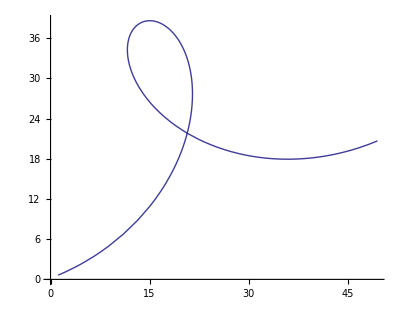

```mathematica
ParametricPlot[15({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3}),{t,-π/2,3π/2}]
```

```mathematica
Round[Table[15({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3}),{t,-π/2,3π/2,π/12}],0.1]
```

{{1.1,0.6},{6.6,3.4},{11.3,7.},{15.3,11.3},{18.3,15.9},{20.4,20.6},{21.4,25.2},{21.4,29.5},{20.7,33.1},{19.3,35.9},{17.5,37.7},{15.6,38.5},{13.9,38.4},{12.5,37.2},{11.7,35.3},{11.8,32.8},{12.8,29.8},{14.8,26.7},{17.8,23.8},{21.8,21.2},{26.6,19.3},{32.,18.2},{37.8,18.},{43.7,18.8},{49.5,20.7}}

```mathematica
StringJoin[("[NSValue valueWithPoint:NSMakePoint("<>ToString[#[[1]]]<>", "<>ToString[#[[2]]]<>")],\n")&/@Round[Table[15({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3}),{t,-π/2,3π/2,π/12}],0.1]]
```

[NSValue valueWithPoint:NSMakePoint(1.1, 0.6)],
[NSValue valueWithPoint:NSMakePoint(6.6, 3.4)],
[NSValue valueWithPoint:NSMakePoint(11.3, 7.)],
[NSValue valueWithPoint:NSMakePoint(15.3, 11.3)],
[NSValue valueWithPoint:NSMakePoint(18.3, 15.9)],
[NSValue valueWithPoint:NSMakePoint(20.4, 20.6)],
[NSValue valueWithPoint:NSMakePoint(21.4, 25.2)],
[NSValue valueWithPoint:NSMakePoint(21.4, 29.5)],
[NSValue valueWithPoint:NSMakePoint(20.7, 33.1)],
[NSValue valueWithPoint:NSMakePoint(19.3, 35.9)],
[NSValue valueWithPoint:NSMakePoint(17.5, 37.7)],
[NSValue valueWithPoint:NSMakePoint(15.6, 38.5)],
[NSValue valueWithPoint:NSMakePoint(13.9, 38.4)],
[NSValue valueWithPoint:NSMakePoint(12.5, 37.2)],
[NSValue valueWithPoint:NSMakePoint(11.7, 35.3)],
[NSValue valueWithPoint:NSMakePoint(11.8, 32.8)],
[NSValue valueWithPoint:NSMakePoint(12.8, 29.8)],
[NSValue valueWithPoint:NSMakePoint(14.8, 26.7)],
[NSValue valueWithPoint:NSMakePoint(17.8, 23.8)],
[NSValue valueWithPoint:NSMakePoint(21.8, 21.2)],
[NSValue valueWithPoint:NSMakePoint(26.6, 19.3)],
[NSValue valueWithPoint:NSMakePoint(32., 18.2)],
[NSValue valueWithPoint:NSMakePoint(37.8, 18.)],
[NSValue valueWithPoint:NSMakePoint(43.7, 18.8)],
[NSValue valueWithPoint:NSMakePoint(49.5, 20.7)],